## 1 Data Import

### import & cleaning

```mathematica
SetDirectory[NotebookDirectory[]];  (* makes it so any files exported will be saved in the same folder that this file is located in *)

dataSpins=Import["C:\\Users\\riiwi\\OneDrive - University of Maine System\\Will\\Data Collection and Analysis\\Surveys F21+F22\\F21+F22 Spins\\F21+F22SpinsNetworkReady.xlsx"][[1]];
dataGriffiths=Import["C:\\Users\\riiwi\\OneDrive - University of Maine System\\Will\\Data Collection and Analysis\\Surveys F21+F22\\F21+F22 Griffiths\\F21+F22GriffithsNetworkReady.xlsx"][[1]];



data=Join[dataSpins,Rest[dataGriffiths]];

Export["F21+F22AllData.xlsx",data]

data//MatrixForm;

data[[1,All]];
data[[All,1]];

(* here we define a number of variables, corresponding to the number of students and the number of concepts and expressions on the survey *)
nStud=Length@data[[All,1]]-1;
nConc=Length@data[[1,All]];
nExp=20;

(* here we initialize the array that will store all of the data. Imagine it as a number of nExp x nExp matrices all stacked on top of each other, one for each student that took the survey. We will essentially create an unweighted adjacency matrix for each student's survey responses and store them here *)
studTab=Table[0,nStud,nExp,nExp];


(* 

below is the code that turns the data table into individual adjacency matrices for each student.  For our case, we're using unweighted matrices, so as to not overweight the connections that may be due to multiple similar concepts on the survey (e.g. multiple versions of "vector" concepts)

Though now that I think of it, I wonder if the real move would be to simply group together concept connections that we deem similar, and treat them as a single weight, while still compounding if there are other (different) concept links between them?  This would generate weighted adjacency matrices while still flattening the redundant concept connections.  Potentially.  Could be worth a look, if the PCA doesn't seem to work great with this "dumber" flattening of the matrices

*)




(* This loop is for the GHD, as it generates an unweighted adjacency matrix for each student.  For the distance from the Wolf paper, we need a wighted adjacency matrix.  Thus, we will comment this out and try a very slightly altered loop to make weighted matrices NOTE: THIS IS INCORRECT--IT'S TRUE THAT THE WOLF PAPER USES WEIGHTED ADJACENCY MATRICES FOR THEIR SUBJECTS, BUT WE DON'T WANT TO HERE AS WE WANT TO FLATTEN THE EFFECT OF MULTIPLE VECTOR-LIKE CONCEPTS BEING PRESENT ON THE SURVEY.  THUS, WE WANT TO GENERATE UNWEIGHTED MATRICES, SO WE *SHOULD* RUN THIS LOOP AND NOT THE FOLLOWING ONE *)

For[i=2,i<=nStud+1,i++,
For[j=1,j<=nConc,j++,
If[Length[LetterNumber[StringDelete[data[[i,j]],","]]]==0,data[[i,j]]={data[[i,j]]}];(* changes all single-letter entries into single-entry lists.  This is done because ContainsAny[] requires a list as input *)
For[k=1,k<=nExp,k++,
For[l=1,l<=nExp,l++,
If[k>l, 
(* this serves to cut the computation time in half. As we know the resulting matrices for each student will be diagonally symmetric, we only compute one off-diagonal *)
If[ContainsAny[LetterNumber[StringDelete[data[[i,j]],","]],{k}]&&ContainsAny[LetterNumber[StringDelete[data[[i,j]],","]],{l}]&&studTab[[i-1,k,l]]==0,studTab[[i-1,k,l]]++]
(* fills out the studTab array with a one the first time a pair of expressions was used together by that student at any point in the survey *)
]
]
]
]
]

(* here is the edited loop, where we don't have it require that an entry is zero before adding to it. This should generate a weighted adjacency matrix for each student   NOTE: THIS IS AN ERROR--WE WANT EACH STUDENT'S INDIVIDUAL NETWORK TO BE UNWEIGHTED, AS THIS SHOULD FLATTEN SOME OF THE EMPHASIS ON VECTOR-LIKE EXPRESSIONS *)

(*
For[i=2,i<=nStud+1,i++,
For[j=1,j<=nConc,j++,
If[Length[LetterNumber[StringDelete[data[[i,j]],","]]]==0,data[[i,j]]={data[[i,j]]}];(* changes all single-letter entries into single-entry lists.  This is done because ContainsAny[] requires a list as input *)
For[k=1,k<=nExp,k++,
For[l=1,l<=nExp,l++,
If[k>l, 
(* this serves to cut the computation time in half. As we know the resulting matrices for each student will be diagonally symmetric, we only compute one off-diagonal *)
If[ContainsAny[LetterNumber[StringDelete[data[[i,j]],","]],{k}]&&ContainsAny[LetterNumber[StringDelete[data[[i,j]],","]],{l}],studTab[[i-1,k,l]]++]
(* fills out the studTab array with a one the first time a pair of expressions was used together by that student at any point in the survey *)
]
]
]
]
]
*)

(* here we add the transpose of each student's matrix to fill out the full matrix *)
For[i=1,i<=nStud,i++,
studTab[[i]]=studTab[[i]]+Transpose[studTab[[i]]]
]




(* here I will subtract out the overconnected networks from the dataset, as well as the unconnected ones.  This means that the "AllData.xlsx" file will include these data, but the "AdjacencyArray.xlsx" file will not *)

overUnConnected={{171},{178},{183},{221},{232},{246},{247},{261},{305},{312},{165},{189}};

Dimensions[studTab]

studTab=Delete[studTab,overUnConnected];

Dimensions[studTab]

Export["F21+F22StudentAdjacencyArray.xlsx",studTab]
```

F21+F22AllData.xlsx

{330,20,20}

{318,20,20}

F21+F22StudentAdjacencyArray.xlsx

### calculate α-index values

318

{}

0

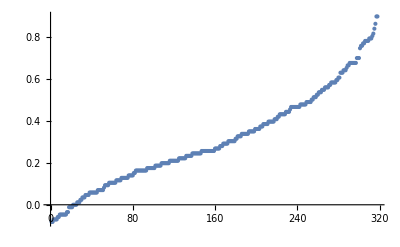

{115,213,58,182,187,203,69,242,45,54,61,67,149,199,266,154,198,71,123,221,279,72,161,194,202,166,281,305,39,163,34,53,274,77,148,214,310,8,17,19,37,169,251,272,304,107,130,146,196,201,239,13,42,102,256,302,16,23,24,64,255,308,316,21,40,84,241,254,48,96,113,121,183,188,189,87,92,172,193,292,2,110,66,83,93,95,164,173,219,252,258,268,277,32,101,132,174,181,226,257,276,15,33,63,128,210,280,104,134,135,153,165,283,295,303,35,43,79,82,129,143,151,248,267,44,81,125,207,223,238,262,65,98,109,209,236,247,5,6,7,41,46,118,216,235,288,60,76,90,111,114,131,136,140,147,150,228,233,264,20,100,208,243,312,126,127,191,55,108,112,141,217,3,14,80,124,152,156,314,10,244,117,215,218,224,36,51,167,176,229,234,287,47,75,133,158,293,307,30,56,99,144,175,4,85,237,29,62,68,282,300,50,116,119,204,250,313,27,103,273,212,220,74,106,120,160,231,253,59,265,275,315,195,9,97,105,159,200,249,260,261,290,70,138,179,184,211,309,57,139,263,294,318,197,285,73,177,317,49,89,86,168,297,1,52,186,28,88,94,190,284,286,18,142,155,206,246,225,296,78,230,170,205,298,122,271,289,270,31,259,26,137,162,178,180,301,311,11,171,306,157,91,240,22,38,12,222,227,232,192,245,278,269,185,291,25,145,299}

{-0.0818713,-0.0818713,-0.0701754,-0.0701754,-0.0701754,-0.0701754,-0.0584795,-0.0584795,-0.0467836,-0.0467836,-0.0467836,-0.0467836,-0.0467836,-0.0467836,-0.0467836,-0.0350877,-0.0350877,-0.0116959,-0.0116959,-0.0116959,-0.0116959,0.,0.,0.,0.,0.0116959,0.0116959,0.0116959,0.0233918,0.0233918,0.0350877,0.0350877,0.0350877,0.0467836,0.0467836,0.0467836,0.0467836,0.0584795,0.0584795,0.0584795,0.0584795,0.0584795,0.0584795,0.0584795,0.0584795,0.0701754,0.0701754,0.0701754,0.0701754,0.0701754,0.0701754,0.0818713,0.0935673,0.0935673,0.0935673,0.0935673,0.105263,0.105263,0.105263,0.105263,0.105263,0.105263,0.105263,0.116959,0.116959,0.116959,0.116959,0.116959,0.128655,0.128655,0.128655,0.128655,0.128655,0.128655,0.128655,0.140351,0.140351,0.140351,0.140351,0.140351,0.152047,0.152047,0.163743,0.163743,0.163743,0.163743,0.163743,0.163743,0.163743,0.163743,0.163743,0.163743,0.163743,0.175439,0.175439,0.175439,0.175439,0.175439,0.175439,0.175439,0.175439,0.187135,0.187135,0.187135,0.187135,0.187135,0.187135,0.19883,0.19883,0.19883,0.19883,0.19883,0.19883,0.19883,0.19883,0.210526,0.210526,0.210526,0.210526,0.210526,0.210526,0.210526,0.210526,0.210526,0.222222,0.222222,0.222222,0.222222,0.222222,0.222222,0.222222,0.233918,0.233918,0.233918,0.233918,0.233918,0.233918,0.245614,0.245614,0.245614,0.245614,0.245614,0.245614,0.245614,0.245614,0.245614,0.25731,0.25731,0.25731,0.25731,0.25731,0.25731,0.25731,0.25731,0.25731,0.25731,0.25731,0.25731,0.25731,0.269006,0.269006,0.269006,0.269006,0.269006,0.280702,0.280702,0.280702,0.292398,0.292398,0.292398,0.292398,0.292398,0.304094,0.304094,0.304094,0.304094,0.304094,0.304094,0.304094,0.315789,0.315789,0.327485,0.327485,0.327485,0.327485,0.339181,0.339181,0.339181,0.339181,0.339181,0.339181,0.339181,0.350877,0.350877,0.350877,0.350877,0.350877,0.350877,0.362573,0.362573,0.362573,0.362573,0.362573,0.374269,0.374269,0.374269,0.385965,0.385965,0.385965,0.385965,0.385965,0.397661,0.397661,0.397661,0.397661,0.397661,0.397661,0.409357,0.409357,0.409357,0.421053,0.421053,0.432749,0.432749,0.432749,0.432749,0.432749,0.432749,0.444444,0.444444,0.444444,0.444444,0.45614,0.467836,0.467836,0.467836,0.467836,0.467836,0.467836,0.467836,0.467836,0.467836,0.479532,0.479532,0.479532,0.479532,0.479532,0.479532,0.491228,0.491228,0.491228,0.491228,0.491228,0.502924,0.502924,0.51462,0.51462,0.51462,0.526316,0.526316,0.538012,0.538012,0.538012,0.549708,0.549708,0.549708,0.561404,0.561404,0.561404,0.561404,0.573099,0.573099,0.584795,0.584795,0.584795,0.584795,0.584795,0.596491,0.596491,0.608187,0.608187,0.631579,0.631579,0.631579,0.643275,0.643275,0.643275,0.654971,0.666667,0.666667,0.678363,0.678363,0.678363,0.678363,0.678363,0.678363,0.678363,0.701754,0.701754,0.701754,0.748538,0.760234,0.760234,0.77193,0.77193,0.783626,0.783626,0.783626,0.783626,0.795322,0.795322,0.795322,0.807018,0.818713,0.842105,0.865497,0.900585,0.900585}

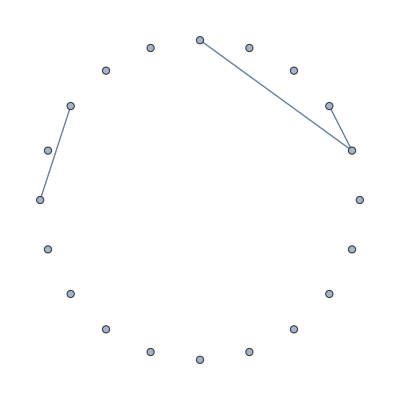

```mathematica
(* this block will go through the students and remove those with too large of α indices (for F21 data, we used α>0.4 as the rule, so I'll keep it consistent here)
Basically, this removes overconnected networks *)
studTab=Round[Import["C:\\Users\\riiwi\\OneDrive - University of Maine System\\Will\\Data Collection and Analysis\\Surveys F21+F22\\F21+F22 All Data\\F21+F22StudentAdjacencyArray.xlsx"]];

nStud=Length@studTab;


Dimensions[studTab];

nEdges=Table[0,nStud];
nExp=20;
α={};

For[i=1,i<=nStud,i++,
nEdges[[i]]=Total[Total[studTab[[i]]]];
α=Append[α,N[(nEdges[[i]]-nExp)/((nExp(nExp-1))/2-(nExp-1))]]
]

BoxWhiskerChart[α];

Length@studTab

αList={};

For[i=1,i<=nStud,i++,
If[α[[i]]>0.94,
αList=Append[αList,i]
]
]

αList

Length@αList

(*Defining the "circle" function.  This is just for making all of the networks share the same morphology for ease of at-a-glance comparison*)
circle[n_]:=Table[{Cos[2*Pi/n*u],Sin[2*Pi/n*u]},{u,1,n}]


AdjacencyGraph[
studTab[[310]],
VertexCoordinates->circle[20]
];


hiαGs=Table[0,Length@αList];

For[i=1,i<=Length@αList,i++,
hiαGs[[i]]=AdjacencyGraph[
studTab[[αList[[i]]]],
VertexCoordinates->circle[20]
]
]

hiαGs;

ListPlot[Sort[α]]

Sort[α];

numLows=20;
lowαGs=Table[0,numLows];

Ordering[α,20];
Sort[α];

For[i=1,i<=numLows,i++,
lowαGs[[i]]=AdjacencyGraph[
studTab[[Ordering[α][[i]]]],
VertexCoordinates->circle[20]
]
]

lowαGs;

Ordering[α]
Sort[α]

AdjacencyGraph[
studTab[[115]],
VertexCoordinates->circle[20]
]
```

```mathematica
studTab=Round[Import["C:\\Users\\riiwi\\OneDrive - University of Maine System\\Will\\Data Collection and Analysis\\Surveys F21+F22\\F21+F22 All Data\\F21+F22StudentAdjacencyArray.xlsx"]];

studTab[[1]]//MatrixForm
```

(0 | 0 | 0 | 0 | 1 | 1 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1
1 | 1 | 0 | 0 | 1 | 0 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 1 | 1 | 0 | 1 | 1 | 1 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1
1 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 1 | 1 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 0 | 1 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1
1 | 1 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 0
1 | 1 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 1 | 1 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0)

## 2 DeltaCon Calculations

```mathematica
SetDirectory[NotebookDirectory[]];  (* makes it so any files exported will be saved in the same folder that this file is located in *)

(* initializing a bunch of things we'll need *)
id=IdentityMatrix[20];
as=Round[Import["C:\\Users\\riiwi\\OneDrive - University of Maine System\\Will\\Data Collection and Analysis\\Surveys F21+F22\\F21+F22 All Data\\F21+F22StudentAdjacencyArray.xlsx"]];
data=Import["C:\\Users\\riiwi\\OneDrive - University of Maine System\\Will\\Data Collection and Analysis\\Surveys F21+F22\\F21+F22 All Data\\F21+F22AllData.xlsx"];
nStud=Length@as
nConc=Length@data[[1,1,All]]
nExp=20

(* generates networks for each student. This is essentially only so we can find vertex degrees for each network *)
gs=Table[0,nStud];
For[i=1,i<=nStud,i++,
gs[[i]]=AdjacencyGraph[as[[i]]]
]

(* generates diagonal square matrices for each student, with the diagonal terms being the degrees of the associated vertices of their networks

Also generates the ϵs, which are a small numbers meant to encode the influence between neighbors for each network *)
ds=Table[0,nStud];
ϵ=Table[0,nStud];
For[i=1,i<=nStud,i++,
ds[[i]]=VertexDegree[gs[[i]]]*id;
ϵ[[i]]=1/(1+Max[VertexDegree[gs[[i]]]])
]

(* calculates the affinity matrices for each student's network.  Effectively, this captures how closely each expression is connected to the others within each network *)
s=Table[0,nStud];
For[i=1,i<=nStud,i++,
s[[i]]=Inverse[id+ϵ[[i]]^2*ds[[i]]-ϵ[[i]]*as[[i]]]
]

N[s[[1]]]//MatrixForm;

(* now we calculate the DeltaCon distances between the students' networks (technically the square, which is why we then square root) *)
dist2=Table[0,nStud,nStud];

For[i=1,i<=nStud,i++,
For[j=1,j<=nStud,j++,
For[k=1,k<=nExp,k++,
For[l=1,l<=nExp,l++,
dist2[[i,j]]=dist2[[i,j]]+(Sqrt[N[s[[i]][[k,l]]]]-Sqrt[N[s[[j]][[k,l]]]])^2
]
]
]
]

dist2//MatrixForm;

dist=Sqrt[dist2];
dist//MatrixForm;

Export["F21+F22DeltaConDistances.xlsx",dist];
```

318

11

20

```mathematica
dist[[1;;10,1;;10]]//MatrixForm
Dimensions[dist]

Dimensions[data]
```

(0. | 3.78001 | 3.39398 | 3.48948 | 3.70412 | 3.8392 | 2.64703 | 3.53324 | 2.57915 | 5.02898
3.78001 | 0. | 5.27832 | 3.12765 | 3.85426 | 3.77943 | 3.71604 | 3.58048 | 5.00154 | 4.39372
3.39398 | 5.27832 | 0. | 5.40038 | 5.18531 | 5.53174 | 4.79807 | 4.8294 | 3.39687 | 6.08682
3.48948 | 3.12765 | 5.40038 | 0. | 4.03821 | 3.88977 | 3.34427 | 3.77437 | 4.78283 | 4.93127
3.70412 | 3.85426 | 5.18531 | 4.03821 | 0. | 4.15009 | 3.70233 | 3.74954 | 4.55441 | 4.66302
3.8392 | 3.77943 | 5.53174 | 3.88977 | 4.15009 | 0. | 2.71989 | 4.06076 | 4.40055 | 4.24742
2.64703 | 3.71604 | 4.79807 | 3.34427 | 3.70233 | 2.71989 | 0. | 4.00916 | 3.70064 | 4.64464
3.53324 | 3.58048 | 4.8294 | 3.77437 | 3.74954 | 4.06076 | 4.00916 | 0. | 4.54339 | 5.20826
2.57915 | 5.00154 | 3.39687 | 4.78283 | 4.55441 | 4.40055 | 3.70064 | 4.54339 | 0. | 4.77847
5.02898 | 4.39372 | 6.08682 | 4.93127 | 4.66302 | 4.24742 | 4.64464 | 5.20826 | 4.77847 | 0.)

{330,330}

## 3 PCA Calculation

318

{318,2}

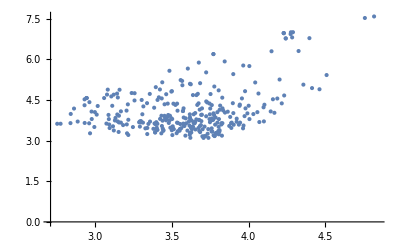

(2.93405
3.65427)

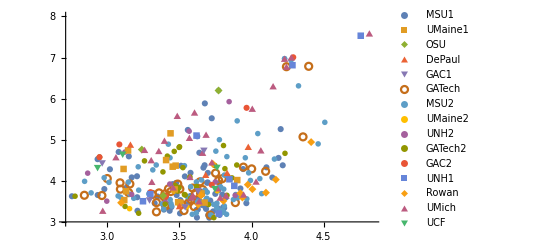

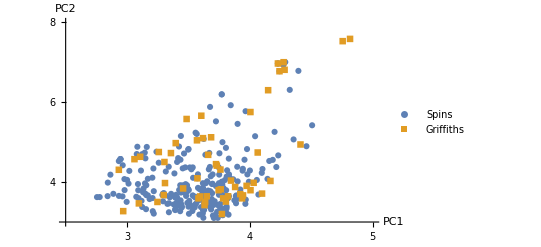

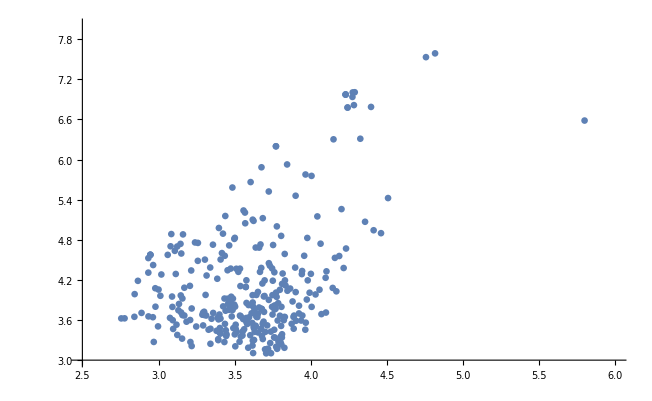

```mathematica
SetDirectory[NotebookDirectory[]];  (* makes it so any files exported will be saved in the same folder that this file is located in *)

dist=Import["C:\\Users\\riiwi\\OneDrive - University of Maine System\\Will\\Data Collection and Analysis\\Surveys F21+F22\\F21+F22 All Data\\F21+F22DeltaConDistances.xlsx"][[1]];

dist[[1;;10,1;;10]]//MatrixForm;

nStud=Length@dist
k=2; (* defines the number of dimensions (PC's) we will preserve *)

(* here we do the SVD and get the three parameters. The GHDs could be found by doing u.σ.ConjugateTranspose[v] *)
{u,σ,v}=SingularValueDecomposition[dist];

(* here we calculate the eigenvalues of the "covariance matrix," which we can use to find the relative variances of the PC's *)
λ=σ.σ/(nStud-1);

(* here we calculate the relative variances of the PC's *)
var=1/Tr[λ]*λ;

var//MatrixForm;

(* here we are effectively reducing our dimensionality to only the first k principal component "directions" *)
uK=u[[All,1;;k]];
σK=σ[[1;;k,1;;k]];
vK=v[[All,1;;k]];

xK=uK.σK.ConjugateTranspose[vK];


v[[All,1]].Transpose[v[[All,4]]];
Transpose[v[[All,2]]].v[[All,1]];


x=u.σ.ConjugateTranspose[v];

xK=xK[[All,1;;k]];


xK[[1;;10,All]]//MatrixForm;

Dimensions[xK]

ListPlot[xK]


(* Order: *)
(*
Spins (273)

MSU21 (McIntyre) 72
UMaine21 (McIntyre) 14
OSU21 (McIntyre) 3
DePaul21 (McIntyre) 5

GAC21 (Townsend) 5
GATech (Townsend) 40

MSU22 (McIntyre) 79
UMaine22 (McIntyre) 5
UNH22 (McIntyre) 11

GATech22 (Townsend) 32
GAC22 (Townsend) 7
*)

(*
Wave functions(57)

UNH21 (Griffiths) 8
Rowan21 (Griffiths) 13

UMich22 (Griffiths) 32
UCF22 (Griffiths) 4
*)

xMcIntyre1=xK[[1;;94]];
xMcIntyre2=xK[[140;;227]];
xMcIntyre=Join[xMcIntyre1,xMcIntyre2];

xTownsend1=xK[[95;;139]];
xTownsend2=xK[[228;;263]];
xTownsend=Join[xTownsend1,xTownsend2];

xSpins=Join[xMcIntyre,xTownsend];

xGriffiths=xK[[264;;318]];

Length@xGriffiths;

xMSU1=xK[[1;;72]];
xUMaine1=xK[[73;;86]];
xOSU=xK[[87;;89]];
xDePaul=xK[[90;;94]];
xGAC1=xK[[95;;99]];
xGATech1=xK[[100;;139]];
xMSU2=xK[[140;;213]];
xUMaine2=xK[[214;;217]];  (* 219-223 *)
xUNH2=xK[[218;;227]]; (* 224-234 *)
xGATech2=xK[[228;;256]]; (* 235-266 *)
xGAC2=xK[[257;;263]];  (* 267-273 *)
xUNH1=xK[[264;;271]]; (* 274-281 *)
xRowan=xK[[272;;284]]; (* 282-294 *)
xUMich=xK[[285;;314]]; (* 295-326 *)
xUCF=xK[[315;;318]]; (* 327-330 *)

xK[[1]]//MatrixForm

ListPlot[
{xMcIntyre,xTownsend,xGriffiths},
PlotLegends->{"McIntyre","Townsend","Griffiths"},
PlotRange->{Automatic,{3,8}},
PlotMarkers->Automatic
];


ListPlot[
{xMSU1,xUMaine1,xOSU,xDePaul,xGAC1,xGATech1,xMSU2,xUMaine2,xUNH2,xGATech2,xGAC2,xUNH1,xRowan,xUMich,xUCF},
PlotLegends->{"MSU1","UMaine1","OSU","DePaul","GAC1","GATech","MSU2","UMaine2","UNH2","GATech2","GAC2","UNH1","Rowan","UMich","UCF"},
PlotRange->{Automatic,{3,8}},
PlotMarkers->Automatic
]

ListPlot[
{xSpins,xGriffiths},
PlotLegends->{"Spins","Griffiths"},
PlotMarkers->Automatic,
AxesLabel->{"PC1","PC2"},
PlotRange->{{2.5,5},{3,8}},
Ticks->{{3,4,5},{4,6,8}},
LabelStyle->18
]

ListPlot[MapIndexed[Tooltip[#1,First@#2]&,xK],PlotRange->{{4.5,6},{3,8}}];

ListPlot[MapIndexed[Tooltip[#1,First@#2]&,xK],PlotRange->{{2.5,6},{3,8}}]

Min[xK];
```

(0.97237 | 0. | 0. | 0. | 0.
0. | 0.0155042 | 0. | 0. | 0.
0. | 0. | 0.00269178 | 0. | 0.
0. | 0. | 0. | 0.00234587 | 0.
0. | 0. | 0. | 0. | 0.00125169)

{318,318}

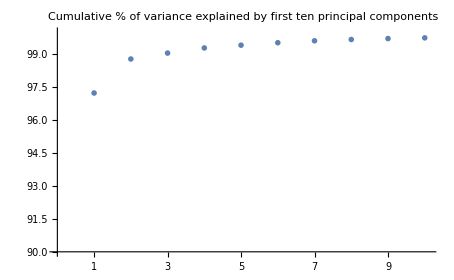

```mathematica
var[[1;;5,1;;5]]//MatrixForm

Dimensions[var]

varList=Diagonal[var];

ListPlot[Accumulate[varList]*100,
PlotRange->{{0,10.1},{90,100}},
PlotMarkers->{"OpenMarkers",Medium},
PlotLabel->"Cumulative % of variance explained\nby first ten principal components",
LabelStyle->18,
Ticks->{{1,2,3,4,5,6,7,8,9,10},Automatic}
]
```

-32.1628+16.7286 y

0.745819

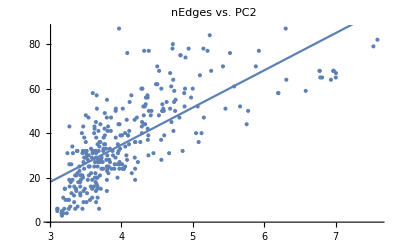

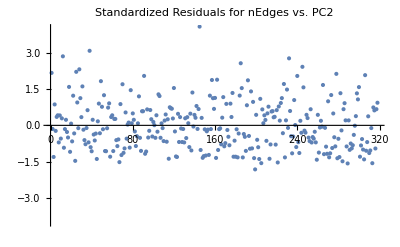

{{3.65427,57},{3.41387,23},{5.0827,36},{3.7648,42},{3.9524,31},{3.50586,31},{3.45497,31},{3.36374,15},{4.59465,50},{4.55723,37},{5.88408,70},{4.31988,77},{3.65376,17},{4.19409,36},{3.29931,26},{3.27078,19},{3.20653,15},{4.2809,60},{3.66452,15},{3.84024,33},{3.63009,20},{5.52192,76},{3.31538,19},{4.1929,19},{5.23797,84},{5.25855,68},{4.70259,45},{3.60021,58},{3.62418,43},{4.11081,41},{4.68392,67},{3.55595,25},{3.94849,26},{3.30204,13},{3.68221,28},{3.76922,39},{3.36181,15},{4.08302,76},{3.33744,12},{3.94624,20},{3.59741,31},{3.29199,18},{4.0801,28},{3.91872,29},{3.3542,6},{3.64645,31},{3.61876,40},{3.43007,21},{3.79908,55},{3.95944,44},{4.37776,39},{4.36675,57},{3.51996,13},{3.10614,6},{4.10782,35},{3.8067,41},{4.32796,52},{3.16152,4},{4.52628,48},{3.51459,32},{3.10164,6},{4.28652,43},{3.27144,26},{3.52985,19},{4.37914,30},{3.80594,24},{3.45539,6},{3.81396,43},{3.1691,5},{3.65796,51},{3.33893,9},{3.25547,10},{4.73879,54},{5.15571,47},{4.28864,40},{3.74606,32},{3.47044,14},{4.50477,62},{3.53066,28},{3.69318,36},{3.47904,29},{3.79053,28},{4.01757,24},{3.46399,20},{4.36889,42},{4.34402,56},{3.63675,22},{6.19811,58},{4.76015,55},{3.38511,32},{4.82745,75},{4.14621,22},{4.19305,24},{4.88057,58},{3.74621,24},{3.35219,21},{4.42211,50},{3.51931,30},{4.72995,41},{3.78736,33},{3.4109,25},{3.39661,18},{4.29051,45},{3.73896,27},{3.92013,50},{3.79623,47},{3.27576,16},{3.95102,35},{3.80414,30},{3.79996,23},{3.68237,32},{3.6674,35},{3.70061,21},{3.64186,32},{3.16676,3},{3.97512,44},{3.64817,38},{3.24459,31},{4.33325,44},{3.54011,47},{3.37242,21},{6.78661,65},{3.47011,9},{3.70597,36},{4.18776,29},{3.69183,34},{4.05514,34},{4.01005,26},{3.71263,28},{3.42456,16},{3.60953,32},{3.82353,25},{4.05211,40},{3.46936,27},{4.23169,27},{3.46189,32},{6.77739,68},{3.9225,51},{5.06933,52},{3.50162,32},{3.77249,35},{4.89163,60},{3.71073,28},{3.8523,41},{3.96783,87},{3.66628,16},{3.5971,32},{3.79701,14},{3.26313,6},{3.96238,32},{4.56071,28},{4.26558,36},{3.67296,27},{3.28472,7},{4.56031,60},{4.19332,36},{4.89871,74},{3.44708,40},{4.38513,50},{3.85554,47},{3.56044,10},{4.52946,68},{3.42646,12},{3.47858,24},{3.63186,27},{3.18549,11},{4.0084,39},{4.36806,56},{3.48848,15},{6.311,64},{5.42372,70},{3.38573,22},{3.72206,24},{4.05341,25},{3.67969,41},{3.98719,39},{4.11577,54},{6.97186,68},{5.4586,51},{6.97186,68},{3.54188,25},{3.18273,4},{3.4386,21},{4.01996,51},{4.72179,80},{4.13968,57},{3.18503,4},{3.45447,21},{3.54436,21},{6.19811,58},{3.31357,34},{5.14944,78},{3.57608,22},{3.26659,10},{3.76751,49},{3.61444,16},{4.34089,53},{3.38727,7},{3.68818,6},{4.57562,50},{3.34043,16},{3.2183,10},{3.23546,4},{3.70645,44},{6.93581,64},{5.00018,60},{3.58835,29},{3.57502,33},{3.54372,30},{3.97205,26},{4.58818,51},{4.07534,46},{3.1677,3},{3.36908,14},{3.75253,38},{3.32178,31},{3.75815,35},{3.92111,38},{3.9723,24},{4.18609,46},{3.64639,9},{5.92648,77},{3.505,29},{3.48048,38},{4.69928,61},{3.66751,25},{5.20696,77},{4.85832,32},{4.0939,39},{4.48508,62},{4.81335,47},{4.38428,77},{3.37702,32},{4.60107,39},{4.66919,31},{4.07074,30},{3.62521,42},{3.64615,29},{3.57173,16},{4.82887,75},{3.65602,20},{3.10372,5},{3.7501,33},{4.37181,37},{4.71599,78},{4.29545,60},{3.88382,30},{3.83003,28},{4.57562,50},{4.32057,44},{3.21076,15},{3.86221,24},{4.21721,47},{3.66579,20},{3.43173,19},{3.42253,18},{3.62157,25},{3.90126,24},{7.00627,67},{4.57562,50},{5.77626,50},{3.72383,29},{4.88546,52},{3.87757,32},{3.50268,48},{3.20059,6},{3.67561,28},{4.03769,24},{7.53097,79},{5.10085,66},{6.81355,65},{3.71179,15},{3.64457,45},{3.42358,13},{4.41224,48},{3.79685,25},{4.0291,24},{4.94234,78},{3.51165,9},{3.90624,26},{3.59249,11},{3.46661,43},{3.69867,27},{6.58289,59},{4.57445,53},{4.74149,59},{4.09451,39},{4.44992,31},{7.00349,65},{4.75322,50},{7.58769,82},{3.81833,22},{5.04676,40},{5.66285,52},{3.84101,27},{5.58137,61},{4.97645,56},{4.72678,64},{6.30224,87},{3.27231,43},{6.97186,68},{3.64072,18},{3.97548,27},{3.59252,15},{3.66718,11},{4.50317,70},{5.12298,40},{3.59255,19},{4.68301,51},{3.64399,14},{6.77739,68},{3.9826,33},{5.75531,44},{3.50235,36},{4.31399,48},{3.79744,19},{4.63422,54},{4.30853,52}}

{318,2}

```mathematica
(* this color codes by number of edges.  In the end, it seems like edge number correlates with PC2 *)
nExp=20;
circle[n_]:=Table[{Cos[2*Pi/n*u],Sin[2*Pi/n*u]},{u,1,n}]
vertexLabels={OverVector["v"],OverHat["j"],OverHat["S_z"],"f(x)","|ψ⟩","|E_2⟩","⟨E_1|","ψ(x)","ψ^*(x)","φ_3(x)","φ_4^*(x)",OverVector["u"]·OverVector["v"],"⟨ψ|ψ⟩","⟨E_3|ψ⟩","∫ψ^*ψdx","∫φ_1^*ψdx","|⟨E_4|ψ⟩|^2","|∫ψ^*ψdx|^2","|∫φ_2^*ψdx|^2","⟨ψ|"};

g[num_]:=AdjacencyGraph[vertexLabels,as[[num]],VertexCoordinates->circle[nExp],VertexLabels->Automatic];

nEdges=Table[0,nStud];

For[i=1,i<=nStud,i++,
nEdges[[i]]=Total[Total[as[[i]]]]/2
]
colorFunc=ColorData[{"SolarColors","Reverse"}];

colorFunc/@Rescale[nEdges];

ListPlot[List/@xK,
PlotStyle->colorFunc/@Rescale[nEdges],
AxesLabel->{"PC1","PC2"},
PlotRange->{{2.5,5},{3,8}},
Ticks->{{3,4,5},{4,6,8}},
LabelStyle->18,
PlotLegends->BarLegend[
{{"SolarColors","Reverse"},MinMax[nEdges]},
LegendLabel->"nEdges"
]
];

ListPlot[Accumulate[varList]*100,
PlotRange->{{0,10.1},{90,100}},
PlotMarkers->{"OpenMarkers",Medium},
PlotLabel->"Cumulative % of variance explained\nby first ten principal components",
LabelStyle->18,
Ticks->{{1,2,3,4,5,6,7,8,9,10},Automatic}
];

BarLegend[
{{"SolarColors","Reverse"},MinMax[nEdges]},
LegendLabel->"nEdges"
];
Dimensions[xK];
Dimensions[nEdges];


plotPC2EdgesList=Transpose[{xK[[All,2]],nEdges}];

ListPlot[plotPC2EdgesList];

model=LinearModelFit[plotPC2EdgesList,y,y];
model["BestFit"]



Correlation[xK[[All,2]],nEdges]

fitFunction[y_]:=16.7286*y-32.1628

Plot[fitFunction[y],{y,0,7},
PlotRange->{{3,7},{0,90}}];

plotPlusFitPC2=Show[
ListPlot[plotPC2EdgesList,
PlotLabel->"nEdges vs. PC2",
LabelStyle->12],
Plot[fitFunction[y],{y,3,7.5}]
];

plotPlusFitPC2

ListPlot[model["StandardizedResiduals"],
PlotLabel->"Standardized Residuals for nEdges vs. PC2",
LabelStyle->12,
PlotRange->{Automatic,{-4,4}}
]

plotPC2EdgesList
Dimensions[plotPC2EdgesList]

Histogram[xK[[All,2]]];
Histogram[nEdges];

g[301];
g[279];
g[29];
g[244];
g[204];
g[282];

g[294];
g[312];
g[171];
```

```mathematica
xK1=xK[[All,1]];
```

```mathematica
Dimensions[xMSU1[[All,1]]]
```

{72}

```mathematica
BoxWhiskerChart[
{xMSU1[[All,1]],xUMaine1[[All,1]],xOSU[[All,1]],xDePaul[[All,1]],xGAC1[[All,1]],xGATech1[[All,1]],xMSU2[[All,1]],xUMaine2[[All,1]],xUNH2[[All,1]],xGATech2[[All,1]],xGAC2[[All,1]],xUNH1[[All,1]],xRowan[[All,1]],xUMich[[All,1]],xUCF[[All,1]]}
];

BoxWhiskerChart[
{xMcIntyre[[All,1]],xTownsend[[All,1]],xGriffiths[[All,1]]}
];

DistributionChart[
{xMcIntyre[[All,1]],xTownsend[[All,1]],xGriffiths[[All,1]]}
];

ListPlot[
{xMcIntyre[[All,1]],xTownsend[[All,1]],xGriffiths[[All,1]]}
];

DistributionChart[
{xSpins[[All,1]],xGriffiths[[All,1]]}
];

BoxWhiskerChart[
{xSpins[[All,1]],xGriffiths[[All,1]]}
];

PairedHistogram[
xSpins[[All,1]],xGriffiths[[All,1]],
{0.3},
"Probability",
ChartLegends->{"spins-first","WF-first"},
ChartStyle->{54,None,None},
PlotLabel->"Normalized distribution of\nPC1 values across curricula",
LabelStyle->20
]

PairedHistogram[
xSpins[[All,2]],xGriffiths[[All,2]],
{0.3},
"Probability",
ChartLegends->{"spins-first","WF-first"},
ChartStyle->{54,None,None},
PlotLabel->"Normalized distribution of\nPC2 values across curricula",
LabelStyle->20
]
```

-Graphics-

-Graphics-

79

67

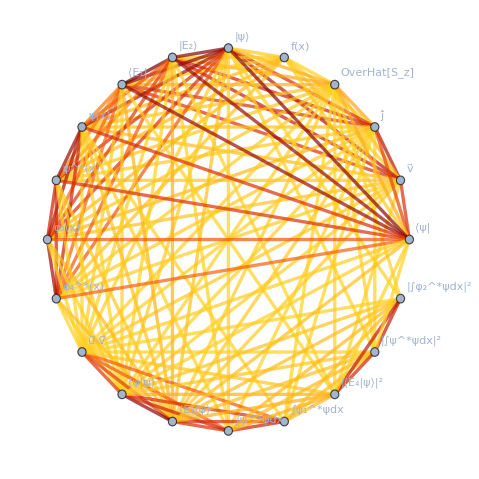

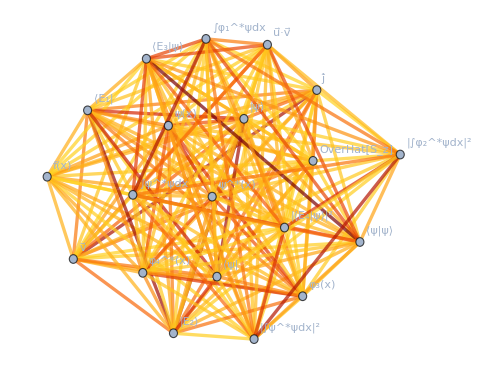

```mathematica
Quantile[xK[[All,1]],{1/4,3/4}];

numlist=Table[i,{i,nStud}];

xKTiles=Transpose[Insert[Transpose[xK],numlist,-1]];

xKTiles//MatrixForm;

(* defines the values that mark the first and fourth quartiles of PC1 *)
firstQ=Quantile[xKTiles[[All,1]],1/4];
fourthQ=Quantile[xKTiles[[All,1]],3/4];


(* 
initializes the lists where I'll store the associated numbers of the students that lie in the first and fourth quartiles of the dataset (along PC1). This will be used to make weighted networks out of just those groups of student networks, to see if there are structural differences (to help suss out what PC1 is)
*)
firstQList=Table[0,Round[nStud/4]];
fourthQList=Table[0,Round[nStud/4]];


(* fills out the QLists with the numbers identifying the students that fall into those quartiles for PC1 *)
j=1;
k=1;
For[i=1,i<=nStud,i++,
If[xKTiles[[i,1]]<=firstQ,
firstQList[[j]]=xKTiles[[i,3]];
j++
];
If[xKTiles[[i,1]]>=fourthQ,
fourthQList[[k]]=xKTiles[[i,3]];
k++
]
]

firstQList;
fourthQList;


firstQAdj=Table[0,nExp,nExp];
fourthQAdj=Table[0,nExp,nExp];

For[i=1,i<=Length@firstQList,i++,
firstQAdj=firstQAdj+as[[firstQList[[i]]]];
fourthQAdj=fourthQAdj+as[[fourthQList[[i]]]];
]

Max[firstQAdj]
Max[fourthQAdj]

For[i=1,i<=nExp,i++,
For[j=1,j<=nExp,j++,
If[firstQAdj[[i,j]]==0,
firstQAdj[[i,j]]=Infinity
];
If[fourthQAdj[[i,j]]==0,
fourthQAdj[[i,j]]=Infinity
]
]
]
firstQAdj//MatrixForm;
fourthQAdj//MatrixForm;


nExp=20;
circle[n_]:=Table[{Cos[2*Pi/n*u],Sin[2*Pi/n*u]},{u,1,n}]
vertexLabels={OverVector["v"],OverHat["j"],OverHat["S_z"],"f(x)","|ψ⟩","|E_2⟩","⟨E_1|","ψ(x)","ψ^*(x)","φ_3(x)","φ_4^*(x)",OverVector["u"]·OverVector["v"],"⟨ψ|ψ⟩","⟨E_3|ψ⟩","∫ψ^*ψdx","∫φ_1^*ψdx","|⟨E_4|ψ⟩|^2","|∫ψ^*ψdx|^2","|∫φ_2^*ψdx|^2","⟨ψ|"};


firstQGraph=WeightedAdjacencyGraph[vertexLabels,firstQAdj];
fourthQGraph=WeightedAdjacencyGraph[vertexLabels,fourthQAdj];


weightList1st=Map[{#,PropertyValue[{firstQGraph,#},EdgeWeight]}&,EdgeList[firstQGraph]];
weightList4th=Map[{#,PropertyValue[{fourthQGraph,#},EdgeWeight]}&,EdgeList[fourthQGraph]];

weightList1st[[All,2]];


graph1st=SetProperty[firstQGraph,{
EdgeStyle->Thread[EdgeList[firstQGraph]->(Directive[Thickness[.005],ColorData[{"SolarColors","Reverse"}][#]]&/@Rescale[weightList1st[[All,2]]])],
VertexCoordinates->circle[nExp],
VertexLabels->Automatic
}]

graph4th=SetProperty[fourthQGraph,{
EdgeStyle->Thread[EdgeList[fourthQGraph]->(Directive[Thickness[.005],ColorData[{"SolarColors","Reverse"}][#]]&/@Rescale[weightList4th[[All,2]]])],
(*VertexCoordinates->circle[nExp],*)
VertexLabels->Automatic
}]

BarLegend[
{{"SolarColors","Reverse"},MinMax[weightList1st[[All,2]]]},
LegendLabel->"first quartile\nedge weights",
LabelStyle->16
]

BarLegend[
{{"SolarColors","Reverse"},MinMax[weightList4th[[All,2]]]},
LegendLabel->"fourth quartile\nedge weights",
LabelStyle->16
]
```

```mathematica
(* this section inverts the edge weights, so that we can use a graphlayout to show which nodes are connected by high edge weights *)

springFirstQAdj=1/firstQAdj;
springFourthQAdj=1/fourthQAdj;

For[i=1,i<=Length@firstQAdj,i++,
For[j=1,j<=Length@firstQAdj,j++,
If[springFirstQAdj[[i,j]]==0,
springFirstQAdj[[i,j]]=Infinity
];
If[springFourthQAdj[[i,j]]==0,
springFourthQAdj[[i,j]]=Infinity
]
]
]

springFirstQGraph=WeightedAdjacencyGraph[vertexLabels,springFirstQAdj];
springFourthQGraph=WeightedAdjacencyGraph[vertexLabels,springFourthQAdj];

graph1stSpring=SetProperty[springFirstQGraph,{
EdgeStyle->Thread[EdgeList[firstQGraph]->(Directive[Thickness[.003],ColorData[{"SolarColors","Reverse"}][#]]&/@Rescale[weightList1st[[All,2]]])],
(*VertexCoordinates->circle[nExp],*)
VertexLabels->Automatic,
GraphLayout->{"SpringElectricalEmbedding","EdgeWeighted"->True}
}];

graph4thSpring=SetProperty[springFourthQGraph,{
EdgeStyle->Thread[EdgeList[fourthQGraph]->(Directive[Thickness[.003],ColorData[{"SolarColors","Reverse"}][#]]&/@Rescale[weightList4th[[All,2]]])],
(*VertexCoordinates->circle[nExp],*)
VertexLabels->Automatic,
GraphLayout->{"SpringElectricalEmbedding","EdgeWeighted"->True}
}];


edgeCountM1st=firstQAdj;
edgeCountM4th=fourthQAdj;


For[i=1,i<=Length@firstQAdj,i++,
For[j=1,j<=Length@firstQAdj,j++,
If[edgeCountM1st[[i,j]]==Infinity,
edgeCountM1st[[i,j]]=0
];
If[edgeCountM4th[[i,j]]==Infinity,
edgeCountM4th[[i,j]]=0
]
]
]

noWeightEdgeCountM1st=Table[0,Length@firstQAdj,Length@firstQAdj];
noWeightEdgeCountM4th=Table[0,Length@firstQAdj,Length@firstQAdj];

For[i=1,i<=Length@firstQAdj,i++,
For[j=1,j<=Length@firstQAdj,j++,
If[edgeCountM1st[[i,j]]!=0,
noWeightEdgeCountM1st[[i,j]]=1
];
If[edgeCountM4th[[i,j]]!=0,
noWeightEdgeCountM4th[[i,j]]=1
]
]
]


edgeCountM1st//MatrixForm;
noWeightEdgeCountM1st//MatrixForm;

nEdges1st=Total[Total[edgeCountM1st]]/2;
nEdges4th=Total[Total[edgeCountM4th]]/2;

noWeightNEdges1st=Total[Total[noWeightEdgeCountM1st]]/2;
noWeightNEdges4th=Total[Total[noWeightEdgeCountM4th]]/2;

α1st=N[(noWeightNEdges1st-20)/((20*(20-1))/2-(20-1))]
α4th=N[(noWeightNEdges4th-20)/((20*(20-1))/2-(20-1))]

MinMax[edgeCountM1st];
MinMax[edgeCountM4th];

weightList1st[[All,2]];

BoxWhiskerChart[
N[{weightList1st[[All,2]],weightList4th[[All,2]]}],
ChartLabels->{"first\nquartile","fourth\nquartile"},
ChartStyle->"Pastel",
LabelStyle->18
];

ListPlot[
N[{Sort[weightList1st[[All,2]]],Sort[weightList4th[[All,2]]]}]
];

Histogram[N[{weightList1st[[All,2]],weightList4th[[All,2]]}],ChartStyle->"Pastel"];

DistributionChart[
N[{weightList1st[[All,2]],weightList4th[[All,2]]}],
ChartStyle->"Pastel",
ChartElementFunction->"HistogramDensity"
];

PairedHistogram[
weightList1st[[All,2]],weightList4th[[All,2]],
ChartLegends->{"first\nquartile","fourth\nquartile"},
ChartStyle->{54,None,None},
PlotLabel->"Distribution of edge weights",
LabelStyle->20
]

PairedHistogram[
weightList1st[[All,2]],weightList4th[[All,2]],
{5},
ChartLegends->{"first\nquartile","fourth\nquartile"},
ChartStyle->{54,None,None},
PlotLabel->"Distribution of edge weights",
LabelStyle->20
];
```

0.730994

0.964912

-Graphics-

(0 | 1 | 0 | 0 | 1 | 1 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
1 | 1 | 0 | 0 | 1 | 0 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 1 | 0 | 0 | 1 | 1 | 0 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
1 | 1 | 0 | 0 | 1 | 1 | 1 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
1 | 1 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0
0 | 1 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

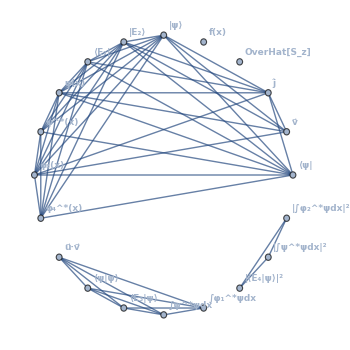

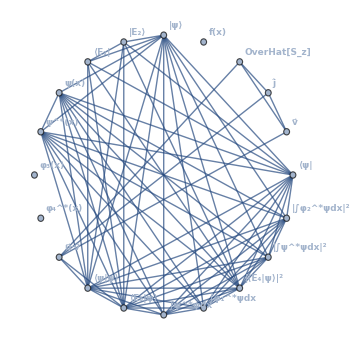

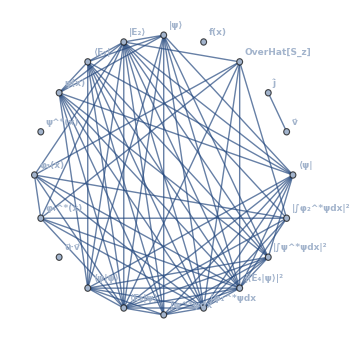

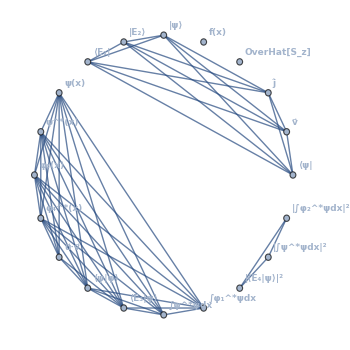

```mathematica
q=Table[RandomVariate[NormalDistribution[RandomInteger[5],1],100],{2},{3}];

q[[1]];
Dimensions[q];

as[[263]]//MatrixForm

AdjacencyGraph[vertexLabels,as[[263]],
VertexCoordinates->circle[nExp],
VertexLabels->Automatic,
VertexLabelStyle->Directive[Bold,9],
ImageSize->350
]

AdjacencyGraph[vertexLabels,as[[157]],
VertexCoordinates->circle[nExp],
VertexLabels->Automatic,
VertexLabelStyle->Directive[Bold,9],
ImageSize->350
]

AdjacencyGraph[vertexLabels,as[[278]],
VertexCoordinates->circle[nExp],
VertexLabels->Automatic,
VertexLabelStyle->Directive[Bold,9],
ImageSize->350
]

AdjacencyGraph[vertexLabels,as[[139]],
VertexCoordinates->circle[nExp],
VertexLabels->Automatic,
VertexLabelStyle->Directive[Bold,9],
ImageSize->350
]
gs[[263]];
gs[[157]];
```

## 4 PCA for subsets

### 4.1 Import, clean, create subsets, calculate DeltaCon

```mathematica
SetDirectory[NotebookDirectory[]];  (* makes it so any files exported will be saved in the same folder that this file is located in *)

(* initializing a bunch of things we'll need *)
id=IdentityMatrix[20];
as=Round[Import["C:\\Users\\riiwi\\OneDrive - University of Maine System\\Will\\Data Collection and Analysis\\Surveys F21+F22\\F21+F22 All Data\\F21+F22StudentAdjacencyArray.xlsx"]];
data=Import["C:\\Users\\riiwi\\OneDrive - University of Maine System\\Will\\Data Collection and Analysis\\Surveys F21+F22\\F21+F22 All Data\\F21+F22AllData.xlsx"][[1]];
nStud=Length@as[[All,1]];
nConc=Length@data[[1,All]];
nExp=20;


(* here we will create the subsets by removing the sections of the adjacency matrices that correspond to connections outside of the single-term expressions (and maybe even the S_z and f(x) ones?) *)

(* initializes the list that will be filled with the adjacency matrices with all of the double-term expressions removed *)
asSing=Table[0,nStud];

(* initializes the number of single-term expressions and the identity matrix to be used *)
nSing=12;
idSing=IdentityMatrix[nSing];

(* here we do the deletion of double-term rows/columns from each student's adjacency matrix *)
For[i=1,i<=nStud,i++,
asSing[[i]]=Drop[Transpose[Drop[as[[i]],{12,19}]],{12,19}]
]

(* generates networks for each student. This is essentially only so we can find vertex degrees for each network *)
gsSing=Table[0,nStud];
For[i=1,i<=nStud,i++,
gsSing[[i]]=AdjacencyGraph[asSing[[i]]]
]

(* generates diagonal square matrices for each student, with the diagonal terms being the degrees of the associated vertices of their networks

Also generates the ϵs, which are a small numbers meant to encode the influence between neighbors for each network *)
dsSing=Table[0,nStud];
ϵSing=Table[0,nStud];
For[i=1,i<=nStud,i++,
dsSing[[i]]=VertexDegree[gsSing[[i]]]*idSing;
ϵSing[[i]]=1/(1+Max[VertexDegree[gsSing[[i]]]])
]

(* calculates the affinity matrices for each student's network.  Effectively, this captures how closely each expression is connected to the others within each network *)
sSing=Table[0,nStud];
For[i=1,i<=nStud,i++,
sSing[[i]]=Inverse[idSing+ϵSing[[i]]^2*dsSing[[i]]-ϵSing[[i]]*asSing[[i]]]
]

(* now we calculate the DeltaCon distances between the students' networks (technically the square, which is why we then square root) *)
dist2Sing=Table[0,nStud,nStud];

For[i=1,i<=nStud,i++,
For[j=1,j<=nStud,j++,
For[k=1,k<=nSing,k++,
For[l=1,l<=nSing,l++,
dist2Sing[[i,j]]=dist2Sing[[i,j]]+(Sqrt[N[sSing[[i]][[k,l]]]]-Sqrt[N[sSing[[j]][[k,l]]]])^2
]
]
]
]

dist2Sing//MatrixForm;

distSing=Sqrt[dist2Sing];

distSing[[1;;10,1;;10]]//MatrixForm

Export["F21+F22DeltaConDistancesSingleTerms.xlsx",distSing];
```

$Aborted

(0. | 4.11067 | 2.21013 | 4.3755 | 4.07893 | 3.81308 | 2.88738 | 3.82519 | 0.843469 | 3.83031
4.11067 | 0. | 5.02173 | 3.7596 | 3.50568 | 2.9778 | 3.14667 | 2.88715 | 4.36514 | 3.58947
2.21013 | 5.02173 | 0. | 5.6447 | 5.04512 | 5.02861 | 4.27156 | 4.42267 | 2.58675 | 5.08619
4.3755 | 3.7596 | 5.6447 | 0. | 4.38471 | 4.35932 | 3.4667 | 4.502 | 4.56313 | 4.42824
4.07893 | 3.50568 | 5.04512 | 4.38471 | 0. | 3.47283 | 3.57818 | 3.27133 | 4.0942 | 3.41725
3.81308 | 2.9778 | 5.02861 | 4.35932 | 3.47283 | 0. | 1.91251 | 3.71571 | 3.73298 | 1.17047
2.88738 | 3.14667 | 4.27156 | 3.4667 | 3.57818 | 1.91251 | 0. | 3.65083 | 2.86537 | 1.80826
3.82519 | 2.88715 | 4.42267 | 4.502 | 3.27133 | 3.71571 | 3.65083 | 0. | 4.15061 | 3.98565
0.843469 | 4.36514 | 2.58675 | 4.56313 | 4.0942 | 3.73298 | 2.86537 | 4.15061 | 0. | 3.65989
3.83031 | 3.58947 | 5.08619 | 4.42824 | 3.41725 | 1.17047 | 1.80826 | 3.98565 | 3.65989 | 0.)

### 4.2 PCA Calculation

```mathematica
SetDirectory[NotebookDirectory[]];  (* makes it so any files exported will be saved in the same folder that this file is located in *)

distSing=Import["C:\\Users\\riiwi\\OneDrive - University of Maine System\\Will\\Data Collection and Analysis\\Surveys F21+F22\\F21+F22 All Data\\F21+F22DeltaConDistancesSingleTerms.xlsx"][[1]];

nStud=Length@distSing;
k=2; (* defines the number of dimensions (PC's) we will preserve *)

(* here we do the SVD and get the three parameters. The GHDs could be found by doing u.σ.ConjugateTranspose[v] *)
{u,σ,v}=SingularValueDecomposition[distSing];

(* here we calculate the eigenvalues of the "covariance matrix," which we can use to find the relative variances of the PC's *)
λ=σ.σ/(nStud-1);

(* here we calculate the relative variances of the PC's *)
var=1/Tr[λ]*λ;

(* here we are effectively reducing our dimensionality to only the first k principal component "directions" *)
uK=u[[All,1;;k]];
σK=σ[[1;;k,1;;k]];
vK=v[[All,1;;k]];

xK=uK.σK.ConjugateTranspose[vK];


v[[All,1]].Transpose[v[[All,4]]];
Transpose[v[[All,2]]].v[[All,1]];


x=u.σ.ConjugateTranspose[v];

xK=xK[[All,1;;k]];


xK[[1;;10,All]]//MatrixForm;

Dimensions[xK];

ListPlot[xK];

var[[1;;5,1;;5]]//MatrixForm
```

(0.945445 | 0. | 0. | 0. | 0.
0. | 0.0344354 | 0. | 0. | 0.
0. | 0. | 0.00765405 | 0. | 0.
0. | 0. | 0. | 0.00355649 | 0.
0. | 0. | 0. | 0. | 0.00254332)

### 4.3 PCA Graphs

```mathematica
xMcIntyre1=xK[[1;;94]];
xMcIntyre2=xK[[140;;227]];
xMcIntyre=Join[xMcIntyre1,xMcIntyre2];

xTownsend1=xK[[95;;139]];
xTownsend2=xK[[228;;263]];
xTownsend=Join[xTownsend1,xTownsend2];

xSpins=Join[xMcIntyre,xTownsend];

xGriffiths=xK[[264;;318]];

(*
ListPlot[
{xMcIntyre,xTownsend,xGriffiths},
PlotLegends->{"McIntyre","Townsend","Griffiths"},
PlotRange->{Automatic,Automatic},
PlotMarkers->Automatic
];

ListPlot[
{xSpins,xGriffiths},
PlotLegends->{"Spins","Griffiths"},
PlotRange->Automatic,
PlotMarkers->Automatic
]

BoxWhiskerChart[
{xMcIntyre[[All,1]],xTownsend[[All,1]],xGriffiths[[All,1]]}
];

DistributionChart[
{xMcIntyre[[All,1]],xTownsend[[All,1]],xGriffiths[[All,1]]}
];

*)
```

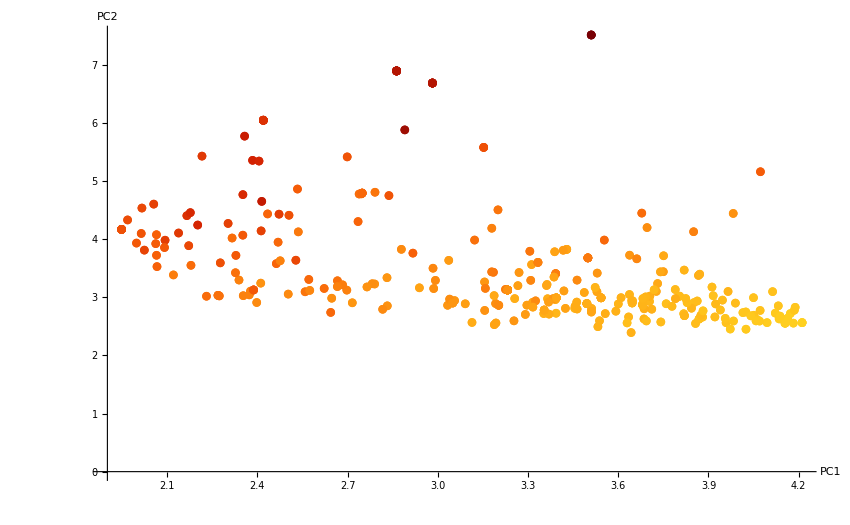

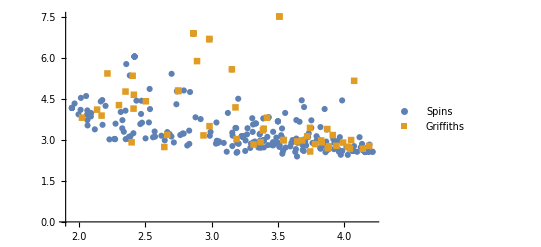

{273,2}

```mathematica
(* this block here color codes the student networks by the numer of edges within them, and shows that it is likely that PC1 is explained by this, or at least that they're roughly correllated? *)
nEdgesSing=Table[0,nStud];

For[i=1,i<=nStud,i++,
nEdgesSing[[i]]=Total[Total[asSing[[i]]]]/2
]
colorFunc=ColorData[{"SolarColors","Reverse"}];

colorFunc/@Rescale[nEdgesSing];

ListPlot[List/@xK,PlotStyle->colorFunc/@Rescale[nEdgesSing],AxesLabel->{"PC1","PC2"},PlotRange->Automatic]

ListPlot[
{xSpins,xGriffiths},
PlotLegends->{"Spins","Griffiths"},
PlotRange->Automatic,
PlotMarkers->Automatic
]
```

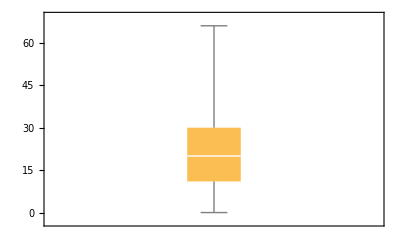

```mathematica
BoxWhiskerChart[nEdgesSing]
```

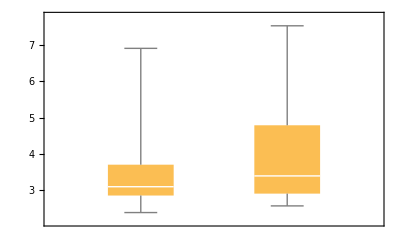

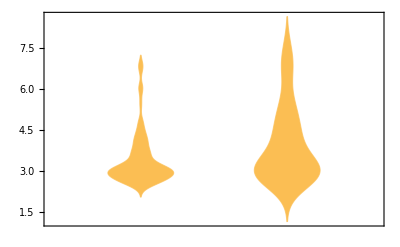

```mathematica
BoxWhiskerChart[
{xMcIntyre[[All,2]],xTownsend[[All,2]],xGriffiths[[All,2]]}
];

DistributionChart[
{xMcIntyre[[All,2]],xTownsend[[All,2]],xGriffiths[[All,2]]}
];

BoxWhiskerChart[
{xSpins[[All,2]],xGriffiths[[All,2]]}
]

DistributionChart[
{xSpins[[All,2]],xGriffiths[[All,2]]}
]
```

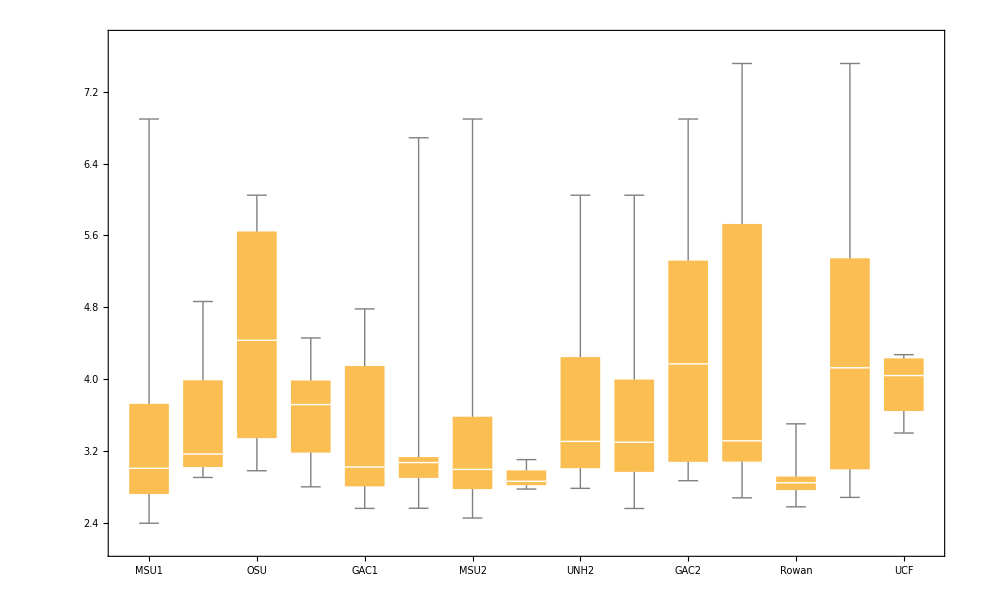

```mathematica
xMSU1=xK[[1;;72]];
xUMaine1=xK[[73;;86]];
xOSU=xK[[87;;89]];
xDePaul=xK[[90;;94]];
xGAC1=xK[[95;;99]];
xGATech1=xK[[100;;139]];
xMSU2=xK[[140;;213]];
xUMaine2=xK[[214;;217]];  (* 219-223 *)
xUNH2=xK[[218;;227]]; (* 224-234 *)
xGATech2=xK[[228;;256]]; (* 235-266 *)
xGAC2=xK[[257;;263]];  (* 267-273 *)
xUNH1=xK[[264;;271]]; (* 274-281 *)
xRowan=xK[[272;;284]]; (* 282-294 *)
xUMich=xK[[285;;314]]; (* 295-326 *)
xUCF=xK[[315;;318]]; (* 327-330 *)


ListPlot[
{xMSU1,xUMaine1,xOSU,xDePaul,xGAC1,xGATech1,xMSU2,xUMaine2,xUNH2,xGATech2,xGAC2,xUNH1,xRowan,xUMich,xUCF},
PlotLegends->{"MSU1","UMaine1","OSU","DePaul","GAC1","GATech","MSU2","UMaine2","UNH2","GATech2","GAC2","UNH1","Rowan","UMich","UCF"},
PlotRange->Automatic,
PlotMarkers->Automatic
];

BoxWhiskerChart[
{xMSU1[[All,2]],xUMaine1[[All,2]],xOSU[[All,2]],xDePaul[[All,2]],xGAC1[[All,2]],xGATech1[[All,2]],xMSU2[[All,2]],xUMaine2[[All,2]],xUNH2[[All,2]],xGATech2[[All,2]],xGAC2[[All,2]],xUNH1[[All,2]],xRowan[[All,2]],xUMich[[All,2]],xUCF[[All,2]]},
ChartLabels->{"MSU1","UMaine1","OSU","DePaul","GAC1","GATech","MSU2","UMaine2","UNH2","GATech2","GAC2","UNH1","Rowan","UMich","UCF"}
]

DistributionChart[
{xMcIntyre[[All,2]],xTownsend[[All,2]],xGriffiths[[All,2]]}
];
```

## 5 PCA for individual concepts

### Data Import, cleaning

```mathematica
SetDirectory[NotebookDirectory[]];  (* makes it so any files exported will be saved in the same folder that this file is located in *)

data=Import["C:\\Users\\riiwi\\OneDrive - University of Maine System\\Will\\Data Collection and Analysis\\Surveys F21+F22\\F21+F22 All Data\\F21+F22AllData.xlsx"][[1]];

(* here I delete the over- and unconnected student data *)
overUnConnected={{171},{178},{183},{221},{232},{246},{247},{261},{305},{312},{165},{189}};
data=Delete[data,overUnConnected+1];

(* here we define a number of variables, corresponding to the number of students and the number of concepts and expressions on the survey *)
nStud=Length@data[[All,1]]-1;
nConc=Length@data[[1,All]];
nExp=20;

adjs=Table[0,nConc,nStud,nExp,nExp];

Timing[

For[i=2,i<=nStud+1,i++,
For[j=1,j<=nConc,j++,
If[Length[LetterNumber[StringDelete[data[[i,j]],","]]]==0,data[[i,j]]={data[[i,j]]}];(* changes all single-letter entries into single-entry lists.  This is done because ContainsAny[] requires a list as input *)
For[k=1,k<=nExp,k++,
For[l=1,l<=nExp,l++,
If[k>l, 
(* this serves to cut the computation time in half. As we know the resulting matrices for each student will be diagonally symmetric, we only compute one off-diagonal *)
If[ContainsAny[LetterNumber[StringDelete[data[[i,j]],","]],{k}]&&ContainsAny[LetterNumber[StringDelete[data[[i,j]],","]],{l}]&&adjs[[j,i-1,k,l]]==0,adjs[[j,i-1,k,l]]++]
(* fills out the studTab array with a one the first time a pair of expressions was used together by that student at any point in the survey *)
]
]
]
]
]

]

(* here I transpose so the first layer is the different concepts, rather than the different students *)
data=Transpose[data];

Dimensions[data]

adjs[[1,1]]//MatrixForm;

Export["F21+F22StudentAdjacencyArraysPerConcept.wxf",adjs];
```

{132.578,Null}

{11,319}

### DeltaCon Calculations

```mathematica
SetDirectory[NotebookDirectory[]];  (* makes it so any files exported will be saved in the same folder that this file is located in *)

adjs=Import["C:\\Users\\riiwi\\OneDrive - University of Maine System\\Will\\Data Collection and Analysis\\Surveys F21+F22\\F21+F22 All Data\\F21+F22StudentAdjacencyArraysPerConcept.wxf"];

(* here we define a number of variables, corresponding to the number of students and the number of concepts and expressions on the survey *)
nConc=Dimensions[adjs][[1]];
nStud=Dimensions[adjs][[2]];
nExp=20;
id=IdentityMatrix[nExp];


(* oops, I forgot to add the transpose to make them diagonally symmetric--I'll do that now *)
For[i=1,i<=nConc,i++,
For[j=1,j<=nStud,j++,
adjs[[i,j]]=adjs[[i,j]]+Transpose[adjs[[i,j]]]
]
]


(* generates networks for each student/concept. This is essentially only so we can find vertex degrees for each network *)
gs=Table[0,nConc,nStud];


For[i=1,i<=nConc,i++,
For[j=1,j<=nStud,j++,
gs[[i,j]]=AdjacencyGraph[adjs[[i,j]]]
]
]

gs[[All,1]];


(* generates diagonal square matrices for each student, with the diagonal terms being the degrees of the associated vertices of their networks

Also generates the ϵs, which are a small numbers meant to encode the influence between neighbors for each network *)
ds=Table[0,nConc,nStud];
ϵ=Table[0,nConc,nStud];
For[j=1,j<=nConc,j++,
For[i=1,i<=nStud,i++,
ds[[j,i]]=VertexDegree[gs[[j,i]]]*id;
ϵ[[j,i]]=1/(1+Max[VertexDegree[gs[[j,i]]]])
]
]


(* calculates the affinity matrices for each student's network.  Effectively, this captures how closely each expression is connected to the others within each network *)
s=Table[0,nConc,nStud];
For[j=1,j<=nConc,j++,
For[i=1,i<=nStud,i++,
s[[j,i]]=Inverse[id+ϵ[[j,i]]^2*ds[[j,i]]-ϵ[[j,i]]*adjs[[j,i]]]
]
]

(* now we calculate the DeltaCon distances between the students' networks (technically the square, which is why we then square root) *)
dist2=Table[0,nConc,nStud,nStud];

Timing[

For[m=1,m<=nConc,m++,
For[i=1,i<=nStud,i++,
For[j=1,j<=nStud,j++,
If[i>j, (* this is just to cut the calculation time in half, as the resultant distances will be symmetric anyway *)
For[k=1,k<=nExp,k++,
For[l=1,l<=nExp,l++,
dist2[[m,i,j]]=dist2[[m,i,j]]+(Sqrt[N[s[[m,i]][[k,l]]]]-Sqrt[N[s[[m,j]][[k,l]]]])^2
]
]
]
]
]
]

]

dist=Sqrt[dist2];

For[i=1,i<=nConc,i++,
dist[[i]]=dist[[i]]+Transpose[dist[[i]]]
]

Export["F21+F22DeltaConDistancesPerConcept.wxf",dist];
```

{1575.41,Null}

```mathematica
data[[All,1]]
```

{Vector,Quantum State,Inner Product,Dot Product,Unit Vector,Basis Vector,Wave Function,Eigenvector,Eigenstate,Probability Amplitude,Probability}

```mathematica
SetDirectory[NotebookDirectory[]];  (* makes it so any files exported will be saved in the same folder that this file is located in *)

Export["F21+F22DeltaConDistancesPerConcept.wxf",dist];
```

### PCA Calculations

```mathematica
SetDirectory[NotebookDirectory[]];  (* makes it so any files exported will be saved in the same folder that this file is located in *)

dist=Import["C:\\Users\\riiwi\\OneDrive - University of Maine System\\Will\\Data Collection and Analysis\\Surveys F21+F22\\F21+F22 All Data\\F21+F22DeltaConDistancesPerConcept.wxf"];

Dimensions[dist]

dist[[1,1;;10,1;;10]]//MatrixForm;

nConc=Length@dist;
nStud=Length@dist[[1]];
k=2; (* defines the number of dimensions (PC's) we will preserve *)

u=Table[0,nConc];
σ=Table[0,nConc];
v=Table[0,nConc];
(* here we do the SVD and get the three parameters. The GHDs could be found by doing u.σ.ConjugateTranspose[v] *)
For[i=1,i<=nConc,i++,
{u[[i]],σ[[i]],v[[i]]}=SingularValueDecomposition[dist[[i]]];
]

λ=Table[0,nConc];
(* here we calculate the eigenvalues of the "covariance matrix," which we can use to find the relative variances of the PC's *)
For[i=1,i<=nConc,i++,
λ[[i]]=σ[[i]].σ[[i]]/(nStud-1)
]

var=Table[0,nConc];
(* here we calculate the relative variances of the PC's *)
For[i=1,i<=nConc,i++,
var[[i]]=1/Tr[λ[[i]]]*λ[[i]];
]

uK=Table[0,nConc];
σK=Table[0,nConc];
vK=Table[0,nConc];
xK=Table[0,nConc];

(* here we are effectively reducing our dimensionality to only the first k principal component "directions" *)
For[i=1,i<=nConc,i++,
uK[[i]]=u[[i,All,1;;k]];
σK[[i]]=σ[[i,1;;k,1;;k]];
vK[[i]]=v[[i,All,1;;k]];

xK[[i]]=uK[[i]].σK[[i]].ConjugateTranspose[vK[[i]]];

xK[[i]]=xK[[i,All,1;;k]];
]
```

{11,318,318}

### PCA graphs & distributions

{11,318,2}

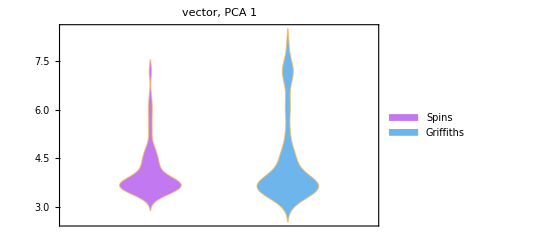
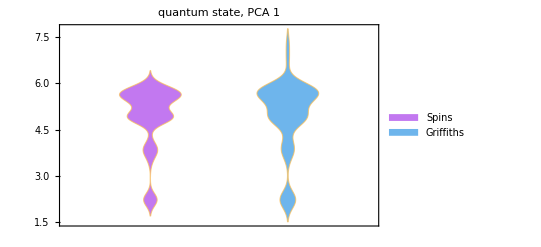
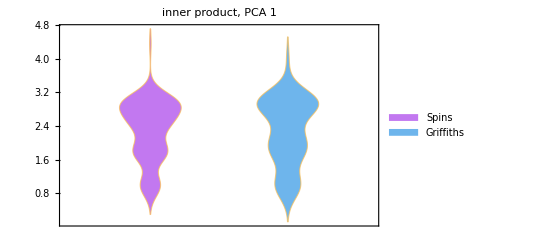
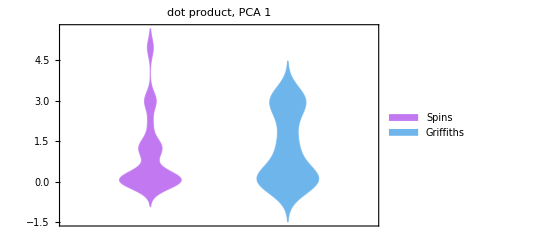
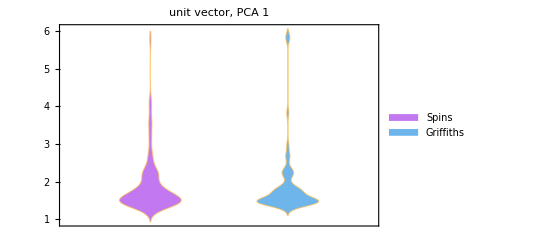
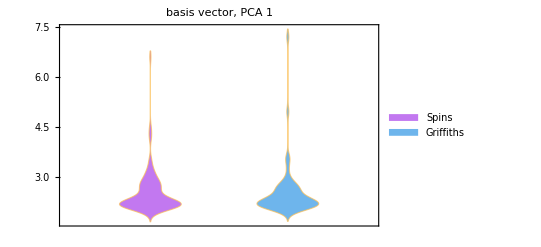
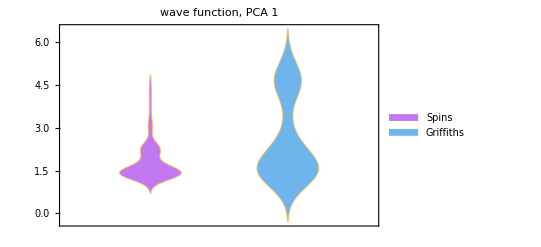
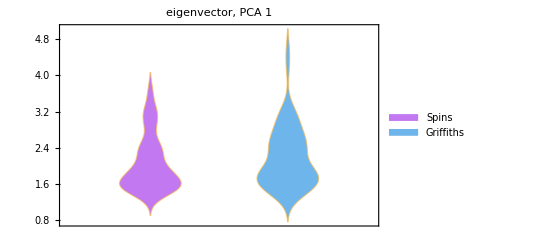

```mathematica
Dimensions[xK]

xMcIntyre1=xK[[All,1;;94]];
xMcIntyre2=xK[[All,140;;227]];
xMcIntyre=Join[xMcIntyre1,xMcIntyre2];

xTownsend1=xK[[All,95;;139]];
xTownsend2=xK[[All,228;;263]];
xTownsend=Join[xTownsend1,xTownsend2];

xSpins=Join[xMcIntyre,xTownsend];

xGriffiths=xK[[All,264;;318]];

listPlots=Table[0,nConc];
boxPlots=Table[0,nConc,k];
distriPlots=Table[0,nConc,k];
histoPlots=Table[0,nConc,k];

concLabels={"vector","quantum state","inner product","dot product","unit vector","basis vector","wave function","eigenvector","eigenstate","probability amplitude","probability"};

ListPlot[xSpins[[7]],
PlotRange->{{0,6},{0,6}}
];
ListPlot[xGriffiths[[7]],
PlotRange->{{0,6},{0,6}}
];


For[i=1,i<=nConc,i++,
listPlots[[i]]=ListPlot[
{xSpins[[i]],xGriffiths[[i]]},
PlotLegends->{"Spins","Griffiths"},
PlotRange->Automatic,
PlotMarkers->Automatic,
PlotLabel->concLabels[[i]]
];

For[j=1,j<=k,j++,
boxPlots[[i,j]]=BoxWhiskerChart[
{xSpins[[i,All,j]],xGriffiths[[i,All,j]]},
PlotLabel->StringJoin[concLabels[[i]],", PCA ",ToString@j],
ChartLegends->{"Spins","Griffiths"},
ChartStyle->"Pastel"
];

distriPlots[[i,j]]=DistributionChart[
{xSpins[[i,All,j]],xGriffiths[[i,All,j]]},
PlotLabel->StringJoin[concLabels[[i]],", PCA ",ToString@j],
ChartLegends->{"Spins","Griffiths"},
ChartStyle->"Pastel"
];

histoPlots[[i,j]]=DistributionChart[
{xSpins[[i,All,j]],xGriffiths[[i,All,j]]},
PlotLabel->StringJoin[concLabels[[i]],", PCA ",ToString@j],
ChartLegends->{"Spins","Griffiths"},
ChartStyle->"Pastel",
ChartElementFunction->"HistogramDensity"
]
]

]

listPlots[[7]];

boxPlots[[All,1]];

distriPlots[[All,1]]
distriPlots[[All,2]]
```

## concept graphs

{11,318,20,20}

32

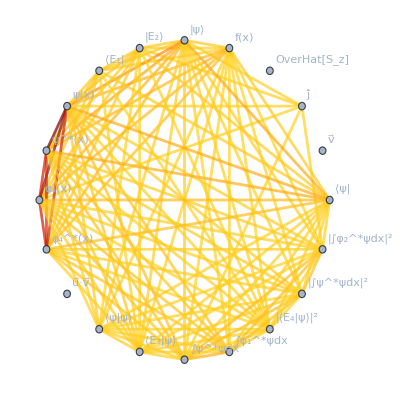

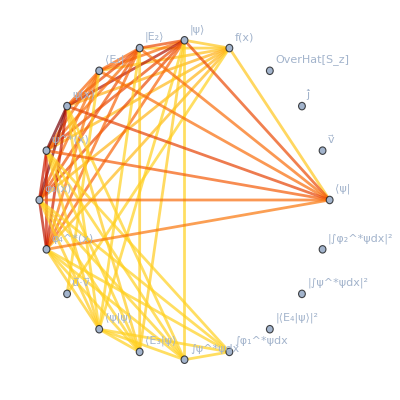

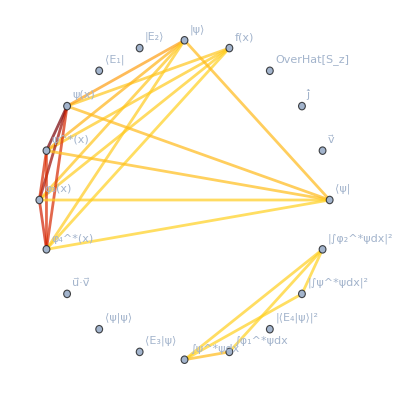

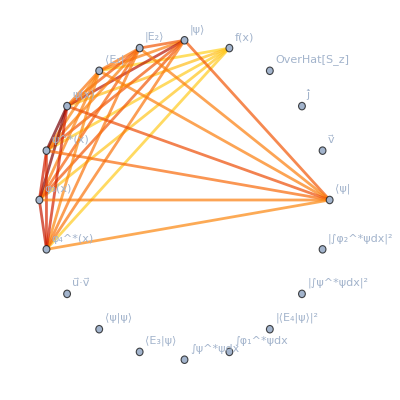

```mathematica
Dimensions[adjs]

(*Defining the "circle" function.  This is just for making all of the networks share the same morphology for ease of at-a-glance comparison*)
circle[n_]:=Table[{Cos[2*Pi/n*u],Sin[2*Pi/n*u]},{u,1,n}]

adjs[[5,1]]//MatrixForm;

Total[adjs[[5,1;;263]]]//MatrixForm;

spinsWFAdj=Total[adjs[[7,1;;263]]];
griffWFAdj=Total[adjs[[7,264;;318]]];

spinsWFAdjCutoff=spinsWFAdj;
griffWFAdjCutoff=griffWFAdj;

spinsCutoff=Max[spinsWFAdj]/10;
griffCutoff=Max[griffWFAdj]/10;

For[i=1,i<=nExp,i++,
For[j=1,j<=nExp,j++,
If[spinsWFAdjCutoff[[i,j]]<spinsCutoff,
spinsWFAdjCutoff[[i,j]]=0
];
If[griffWFAdjCutoff[[i,j]]<griffCutoff,
griffWFAdjCutoff[[i,j]]=0
]
]
]


Max[griffWFAdj]

For[i=1,i<=nExp,i++,
For[j=1,j<=nExp,j++,
If[spinsWFAdj[[i,j]]==0,
spinsWFAdj[[i,j]]=Infinity
];
If[griffWFAdj[[i,j]]==0,
griffWFAdj[[i,j]]=Infinity
];
If[spinsWFAdjCutoff[[i,j]]==0,
spinsWFAdjCutoff[[i,j]]=Infinity
];
If[griffWFAdjCutoff[[i,j]]==0,
griffWFAdjCutoff[[i,j]]=Infinity
]
]
]

vLabels={OverVector["v"],OverHat["j"],OverHat["S_z"],"f(x)","|ψ⟩","|E_2⟩","⟨E_1|","ψ(x)","ψ^*(x)","φ_3(x)","φ_4^*(x)",OverVector["u"]·OverVector["v"],"⟨ψ|ψ⟩","⟨E_3|ψ⟩","∫ψ^*ψdx","∫φ_1^*ψdx","|⟨E_4|ψ⟩|^2","|∫ψ^*ψdx|^2","|∫φ_2^*ψdx|^2","⟨ψ|"};



spinsWFG=WeightedAdjacencyGraph[vLabels,spinsWFAdj];
griffWFG=WeightedAdjacencyGraph[vLabels,griffWFAdj];

spinsWFGCutoff=WeightedAdjacencyGraph[vLabels,spinsWFAdjCutoff];
griffWFGCutoff=WeightedAdjacencyGraph[vLabels,griffWFAdjCutoff];


wListSpinsWF=Map[{#,PropertyValue[{spinsWFG,#},EdgeWeight]}&,EdgeList[spinsWFG]];
wListGriffWF=Map[{#,PropertyValue[{griffWFG,#},EdgeWeight]}&,EdgeList[griffWFG]];

wListSpinsWFCutoff=Map[{#,PropertyValue[{spinsWFGCutoff,#},EdgeWeight]}&,EdgeList[spinsWFGCutoff]];
wListGriffWFCutoff=Map[{#,PropertyValue[{griffWFGCutoff,#},EdgeWeight]}&,EdgeList[griffWFGCutoff]];


spinsWFG=SetProperty[spinsWFG,{VertexSize->0.15,
VertexCoordinates->circle[nExp],EdgeStyle->Thread[EdgeList[spinsWFG]->(Directive[Thickness[.005],ColorData[{"SolarColors","Reverse"}][#]]&/@Rescale[wListSpinsWF[[All,2]]])],
VertexLabels->Automatic
}]

griffWFG=SetProperty[griffWFG,{VertexSize->0.15,
VertexCoordinates->circle[nExp],EdgeStyle->Thread[EdgeList[griffWFG]->(Directive[Thickness[.005],ColorData[{"SolarColors","Reverse"}][#]]&/@Rescale[wListGriffWF[[All,2]]])],
VertexLabels->Automatic
}]

spinsWFGCutoff=SetProperty[spinsWFGCutoff,{VertexSize->0.15,
VertexCoordinates->circle[nExp],EdgeStyle->Thread[EdgeList[spinsWFGCutoff]->(Directive[Thickness[.005],ColorData[{"SolarColors","Reverse"}][#]]&/@Rescale[wListSpinsWFCutoff[[All,2]]])],
VertexLabels->Automatic
}]

griffWFG=SetProperty[griffWFGCutoff,{VertexSize->0.15,
VertexCoordinates->circle[nExp],EdgeStyle->Thread[EdgeList[griffWFGCutoff]->(Directive[Thickness[.005],ColorData[{"SolarColors","Reverse"}][#]]&/@Rescale[wListGriffWFCutoff[[All,2]]])],
VertexLabels->Automatic
}]
```

```mathematica
spinsWFAdj//MatrixForm
griffWFAdj//MatrixForm

Max[spinsWFAdj]
```

(∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | 1 | 1 | ∞ | 1 | ∞ | 1 | ∞ | ∞ | ∞ | ∞ | 1 | ∞ | ∞ | ∞ | 1 | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | 9 | 4 | 3 | 25 | 23 | 21 | 18 | ∞ | 1 | 2 | 2 | 1 | 1 | 1 | 1 | 7
∞ | 1 | ∞ | 9 | ∞ | 8 | 7 | 57 | 41 | 27 | 22 | ∞ | 5 | 5 | 8 | 2 | 3 | 3 | 3 | 36
∞ | 1 | ∞ | 4 | 8 | ∞ | 9 | 10 | 8 | 10 | 8 | ∞ | 1 | 2 | ∞ | ∞ | 1 | ∞ | ∞ | 7
∞ | ∞ | ∞ | 3 | 7 | 9 | ∞ | 8 | 8 | 8 | 8 | ∞ | ∞ | 1 | ∞ | ∞ | 1 | ∞ | ∞ | 7
∞ | 1 | ∞ | 25 | 57 | 10 | 8 | ∞ | 162 | 148 | 121 | ∞ | 7 | 11 | 16 | 14 | 3 | 7 | 4 | 36
∞ | ∞ | ∞ | 23 | 41 | 8 | 8 | 162 | ∞ | 121 | 119 | ∞ | 4 | 9 | 13 | 10 | 3 | 7 | 6 | 33
∞ | 1 | ∞ | 21 | 27 | 10 | 8 | 148 | 121 | ∞ | 126 | ∞ | 2 | 5 | 11 | 13 | 1 | 4 | 3 | 20
∞ | ∞ | ∞ | 18 | 22 | 8 | 8 | 121 | 119 | 126 | ∞ | ∞ | ∞ | 4 | 11 | 12 | 1 | 4 | 3 | 18
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | 1 | 5 | 1 | ∞ | 7 | 4 | 2 | ∞ | ∞ | ∞ | 5 | 5 | 3 | 2 | 1 | 1 | 4
∞ | ∞ | ∞ | 2 | 5 | 2 | 1 | 11 | 9 | 5 | 4 | ∞ | 5 | ∞ | 4 | 4 | 4 | 3 | 1 | 4
∞ | 1 | ∞ | 2 | 8 | ∞ | ∞ | 16 | 13 | 11 | 11 | ∞ | 5 | 4 | ∞ | 35 | 1 | 17 | 19 | 3
∞ | ∞ | ∞ | 1 | 2 | ∞ | ∞ | 14 | 10 | 13 | 12 | ∞ | 3 | 4 | 35 | ∞ | 1 | 16 | 17 | 2
∞ | ∞ | ∞ | 1 | 3 | 1 | 1 | 3 | 3 | 1 | 1 | ∞ | 2 | 4 | 1 | 1 | ∞ | 2 | 1 | 3
∞ | ∞ | ∞ | 1 | 3 | ∞ | ∞ | 7 | 7 | 4 | 4 | ∞ | 1 | 3 | 17 | 16 | 2 | ∞ | 17 | 2
∞ | 1 | ∞ | 1 | 3 | ∞ | ∞ | 4 | 6 | 3 | 3 | ∞ | 1 | 1 | 19 | 17 | 1 | 17 | ∞ | 1
∞ | ∞ | ∞ | 7 | 36 | 7 | 7 | 36 | 33 | 20 | 18 | ∞ | 4 | 4 | 3 | 2 | 3 | 2 | 1 | ∞)

(∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | 3 | 3 | 4 | 7 | 5 | 6 | 5 | 1 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 3
∞ | ∞ | ∞ | 3 | ∞ | 19 | 15 | 27 | 19 | 19 | 16 | ∞ | 1 | 2 | 1 | ∞ | ∞ | ∞ | ∞ | 19
∞ | ∞ | ∞ | 3 | 19 | ∞ | 16 | 19 | 15 | 18 | 16 | ∞ | 1 | 2 | ∞ | ∞ | ∞ | ∞ | ∞ | 15
∞ | ∞ | ∞ | 4 | 15 | 16 | ∞ | 16 | 14 | 15 | 14 | 1 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 15
∞ | ∞ | ∞ | 7 | 27 | 19 | 16 | ∞ | 32 | 31 | 25 | ∞ | 1 | 2 | 1 | ∞ | ∞ | ∞ | ∞ | 20
∞ | ∞ | ∞ | 5 | 19 | 15 | 14 | 32 | ∞ | 25 | 24 | ∞ | 2 | 1 | 1 | 1 | ∞ | ∞ | ∞ | 17
∞ | ∞ | ∞ | 6 | 19 | 18 | 15 | 31 | 25 | ∞ | 26 | ∞ | 2 | 1 | 1 | 1 | ∞ | ∞ | ∞ | 15
∞ | ∞ | ∞ | 5 | 16 | 16 | 14 | 25 | 24 | 26 | ∞ | ∞ | 2 | 1 | 1 | 1 | ∞ | ∞ | ∞ | 14
∞ | ∞ | ∞ | 1 | ∞ | ∞ | 1 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | 1 | 1 | ∞ | 1 | 2 | 2 | 2 | ∞ | ∞ | 1 | 1 | 1 | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | 2 | 2 | ∞ | 2 | 1 | 1 | 1 | ∞ | 1 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | 1 | ∞ | ∞ | 1 | 1 | 1 | 1 | ∞ | 1 | ∞ | ∞ | 1 | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 1 | 1 | ∞ | 1 | ∞ | 1 | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | 3 | 19 | 15 | 15 | 20 | 17 | 15 | 14 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞)

∞